```mathematica
nrdd=Function[{n,x,h},
m=(n-1)/2;
s[k_]:=If[k>m,0,If[k==m,1,((2n-10)s[k+1]-(n+2k+3)s[k+2])/(n -2k-1)]];
1/(2^(n-3)h^2)(s[0]f[x-m h]+∑_(k=1)^m s[k](f[x-(m+k)h]+f[x-(m-k)h]))
];
```

```mathematica
nrdd[7,x,h]
```

(f[x]+f[-6 h+x]-f[-4 h+x]-4 f[-3 h+x]-f[-2 h+x]+2 (f[-5 h+x]+f[-h+x]))/(16 h^2)

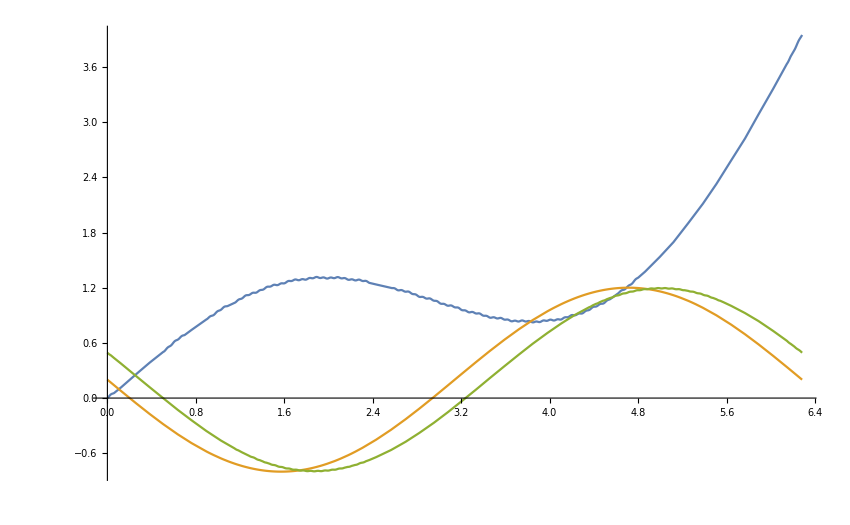

```mathematica
g[x_]:=Sin[x]+x^2/10;
f[x_]:=g[x]+Sin[x*64]*Sin[x*34]/100;
fd1[x_,h_]:=(-f[x-1h]+f[x])/h;
fd2[x_,h_]:=(f[x-2h]-4f[x-1h]+3f[x])/(2h);
fd3[x_,h_]:=(-2f[x-3h]+9f[x-2h]-18f[x-1h]+11f[x])/(6h);
osd5[x_,h_]:=(-f[x-5h]-3f[x-4h]-2f[x-3h]+2f[x-2h]+3f[x-1h]+f[x])/(16h);
ohd5[x_,h_]:=(9f[x-5h]-6f[x-4h]-10f[x-3h]-10f[x-2h]+1f[x-1h]+16f[x])/(28h);


fdd2[x_,h_]:=(f[x-2h]-2f[x-1h]+1f[x])/h^2;
fdd3[x_,h_]:=(-f[x-3h]+4f[x-2h]-5f[x-1h]+2f[x])/h^2;
fdd4[x_,h_]:=(11f[x-4h]-56f[x-3h]+114f[x-2h]-104f[x-1h]+35f[x])/(12 h^2);
nrdd7[x_,h_]:=((f[x-3h]+f[x+3h])+2(f[x-2h]+f[x+2h])-(f[x-1h]+f[x+1h])-4f[x])/(16 h^2);
osdd5[x_,h_]:=(-osd5[x-5h,h]-3osd5[x-4h,h]-2osd5[x-3h,h]+2osd5[x-2h,h]+3osd5[x-1h,h]+osd5[x,h])/(16h);
ohdd5[x_,h_]:=(-ohd5[x-5h,h]-3ohd5[x-4h,h]-2ohd5[x-3h,h]+2ohd5[x-2h,h]+3ohd5[x-1h,h]+ohd5[x,h])/(16h);
(*Plot[{f[x],g'[x],ohd5[x,0.1]},{x,0,2Pi}]*)
Plot[{f[x],g''[x],nrdd[7,x,0.1]},{x,0,2Pi}]
```